## U^long(r,r',θ), long range part of U(r, r’), analytic form

```mathematica
θ=Pi/4;
σA=Sqrt[50/4];
fP=1;
```

```mathematica
Ulong[r_,rp_,f_]=(2 f^2)/(ⅈ π Sin[2θ] Cos[θ]^2)(Cos[(r+rp)^2/(2 Sin[2θ])]+Cos[(r-rp)^2/(2 Sin[2θ])])
```

-(4 ⅈ f^2 (Cos[1/2 (r-rp)^2]+Cos[1/2 (r+rp)^2]))/π

```mathematica
psi[rp_]=1/(Sqrt[2 Pi]σA)Exp[-rp^2/(4 σA^2)]
```

(ⅇ^(-rp^2/50))/(5 √π)

```mathematica
(*psi[rp_]=1*)
```

```mathematica
(*interaction[r_,f_]=Integrate[Ulong[r,rp,f]*psi[rp]^2,{rp,-∞,∞},Assumptions-> rp ∈ Reals&&r∈Reals]*)
```

```mathematica
interaction[r_,f_]=-(4 ⅈ √(2/629) ⅇ^((-25/629-(2 ⅈ)/629) r^2) (√(2-25 ⅈ)+√(2+25 ⅈ) ⅇ^((4 ⅈ r^2)/629)) f^2)/(5 π^(3/2));
```

```mathematica
flatinteraction[r_,f_]=Integrate[Ulong[r,rp,f],{rp,-∞,∞},Assumptions->r∈Reals&&rp∈Reals]
```

-(8 ⅈ f^2)/(√π)

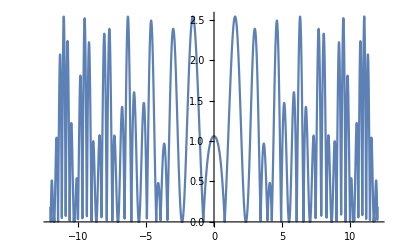

```mathematica
Plot[Abs[Ulong[r,2]],{r,-12,12}]
```

1000

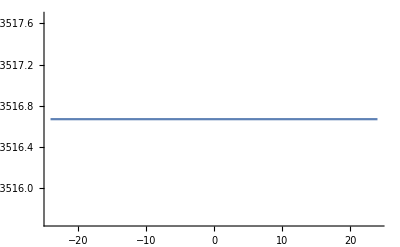

```mathematica
FF=1000
Plot[Abs[flatinteraction[r,FF]],{r,-24,24},PlotRange->Full]
```

```mathematica
.
```